```mathematica
Needs["Wolfram`QuantumFramework`"]

ClearAll[ϕ,Rotaciones,CZcapa,ListaAnsatzDatos,Ansatz1,ConoCausal,DibujarConoCausal];
ϕ[n_]:=QuantumState[StringRepeat["0",n]];

Rotaciones[angulos_List]:=Table[QuantumOperator["RY"[angulos[[j]]],{j-1}],{j,Length[angulos]}];

CZcapa[n_]:=Table[QuantumOperator["CZ",{j-1,j}],{j,1,n-1}];

ListaAnsatzDatos[n_Integer,params_List]:=Module[{θ,ϕpar},θ=Take[params,n];
ϕpar=Take[params,{n+1,2 n}];
Join[(*Primera capa de RY*)Table[<|"Gate"->QuantumOperator["RY"[θ[[j+1]]],{j}],"Qubits"->{j},"Label"->"RY"|>,{j,0,n-1}],(*Capa CZ*)Table[<|"Gate"->QuantumOperator["CZ",{j,j+1}],"Qubits"->{j,j+1},"Label"->"CZ"|>,{j,0,n-2}],(*Segunda capa de RY*)Table[<|"Gate"->QuantumOperator["RY"[ϕpar[[j+1]]],{j}],"Qubits"->{j},"Label"->"RY"|>,{j,0,n-1}]]];


Ansatz1[n_Integer,params_List]:=QuantumCircuitOperator[ListaAnsatzDatos[n,params][[All,"Gate"]]];


ConoCausal[lista_List,qubitsIniciales_List]:=Module[{cono=Union[qubitsIniciales],capas,usadas={},gatesCapa,qubitsNuevos,qGate,layerGate},(*Obtener las capas existentes*)capas=Reverse[Sort[DeleteDuplicates[Lookup[lista,"Layer"]]]];
(*Recorrer desde la última capa hacia la primera*)Do[gatesCapa=Select[Range[Length[lista]],lista[[#]]["Layer"]==capa&];
qubitsNuevos={};
Do[qGate=lista[[i]]["Qubits"];
If[Intersection[qGate,cono]=!={},AppendTo[usadas,i];
qubitsNuevos=Union[qubitsNuevos,qGate];],{i,gatesCapa}];
(*Solo después de revisar toda la capa ampliamos el cono*)cono=Union[cono,qubitsNuevos];,{capa,capas}];
<|"Qubits"->cono,"GateIndices"->Sort[usadas]|>]

Clear[DibujarConoCausal]

DibujarConoCausal[lista_List,observable_List]:=Module[{datos,gatesCono,qubitLists,layers,n,maxLayer,dx=2.5,elementos={},qubits,layer,x,color},(*Datos del circuito*)qubitLists=Lookup[lista,"Qubits"];
layers=Lookup[lista,"Layer"];
n=Max[Flatten[qubitLists]]+1;
maxLayer=Max[layers];
(*Cono causal*)datos=ConoCausalPorCapas[lista,observable];
gatesCono=datos["GateIndices"];
(*Líneas de qubits*)Do[AppendTo[elementos,{GrayLevel[0.65],Line[{{0,-q},{dx (maxLayer+1),-q}}],White,Text[Style["q"<>ToString[q],12],{-0.4,-q}]}],{q,0,n-1}];
(*Gates*)Do[qubits=lista[[i]]["Qubits"];
layer=lista[[i]]["Layer"];
x=dx layer;
color=If[MemberQ[gatesCono,i],Red,GrayLevel[0.65]];
If[Length[qubits]==1,(*Gate de un qubit*)AppendTo[elementos,Inset[Framed[Style[lista[[i]]["Label"],10,color],Background->White,FrameStyle->color,FrameMargins->Tiny],{x,-First[qubits]}]],(*Gate de dos qubits*)AppendTo[elementos,{color,Thick,Line[{{x,-qubits[[1]]},{x,-qubits[[2]]}}],Disk[{x,-qubits[[1]]},0.07],Disk[{x,-qubits[[2]]},0.07]}]],{i,Length[lista]}];
(*Observable*)Do[AppendTo[elementos,{Red,Disk[{dx (maxLayer+1),-q},0.09],Text[Style["O",12,Bold,Red],{dx (maxLayer+1)+0.35,-q}]}],{q,observable}];
(* =======================================*)(*Frontera punteada del cono causal*)(* =======================================*)capasOrdenadas=Sort@DeleteDuplicates[Lookup[lista,"Layer"]];
conoActual=Union[observable];
soportePorCapa=<||>;

(*soporte final*)
soportePorCapa[maxLayer+1]=conoActual;

(*recorrer hacia atrás*)
Do[gatesCapa=Select[Range[Length[lista]],lista[[#,"Layer"]]==layer&];
nuevos={};
Do[If[Intersection[lista[[i,"Qubits"]],conoActual]=!={},nuevos=Union[nuevos,lista[[i,"Qubits"]]]],{i,gatesCapa}];
conoActual=Union[conoActual,nuevos];
soportePorCapa[layer]=conoActual;,{layer,Reverse[capasOrdenadas]}];

puntosSuperior={};
puntosInferior={};

Do[soporte=soportePorCapa[layer];
If[Length[soporte]>0,AppendTo[puntosSuperior,{dx*layer,-Min[soporte]+0.35}];
AppendTo[puntosInferior,{dx*layer,-Max[soporte]-0.35}];],{layer,capasOrdenadas}];

(*punto final en el observable*)
AppendTo[puntosSuperior,{dx*(maxLayer+1),-Min[observable]+0.35}];

AppendTo[puntosInferior,{dx*(maxLayer+1),-Max[observable]-0.35}];

(*añadir contorno al dibujo*)
AppendTo[elementos,{Red,Dashed,Thick,Line[Join[puntosSuperior,Reverse[puntosInferior],{First[puntosSuperior]}]]}];
Graphics[elementos,Axes->False,ImageSize->900,PlotRange->All,PlotRangePadding->0.5,AspectRatio->0.45]]
Clear[TamanoConoCausal]

TamanoConoCausal[lista_List,obs_List]:=Module[{datos},datos=ConoCausal[lista,obs];
If[AssociationQ[datos],Length[datos["Qubits"]],$Failed]]
Clear[MetricasLocalidad]

MetricasLocalidad[lista_List,obs:{k_Integer}]:=Module[{datos,qubitsCono,tamano,n,fraccion,radio,gates,capas,profundidad},datos=ConoCausal[lista,obs];
qubitsCono=datos["Qubits"];
gates=datos["GateIndices"];
n=1+Max[Flatten[Lookup[lista,"Qubits"]]];
tamano=Length[qubitsCono];
fraccion=N[tamano/n];
radio=Max[Abs[qubitsCono-k]];
capas=DeleteDuplicates[Lookup[lista[[gates]],"Layer"]];
profundidad=Length[capas];
Dataset[<|"Observable"->k,"Qubits totales"->n,"Qubits en el cono"->qubitsCono,"Tamaño del cono"->tamano,"Fracción del sistema"->fraccion,"Radio espacial"->radio,"Profundidad efectiva"->profundidad|>]]
Clear[DatosLocalidad]

DatosLocalidad[lista_List,obs:{k_Integer}]:=Module[{datos,qubitsCono,tamano,n,fraccion,radio,gates,capas,profundidad},datos=ConoCausal[lista,obs];
qubitsCono=datos["Qubits"];
gates=datos["GateIndices"];
n=1+Max[Flatten[Lookup[lista,"Qubits"]]];
tamano=Length[qubitsCono];
fraccion=N[tamano/n];
radio=Max[Abs[qubitsCono-k]];
capas=DeleteDuplicates[Lookup[lista[[gates]],"Layer"]];
profundidad=Length[capas];
<|"Observable"->"q"<>ToString[k],"Qubits totales"->n,"Qubits en el cono"->qubitsCono,"Tamaño del cono"->tamano,"Fracción del sistema"->NumberForm[fraccion,{3,2}],"Radio espacial"->radio,"Profundidad efectiva"->profundidad|>]
Clear[MostrarConoCausal]

MostrarConoCausal[lista_List,obs:{k_Integer}]:=Module[{dibujo,datos,filas,tabla},dibujo=DibujarConoCausal[lista,obs];
datos=DatosLocalidad[lista,obs];
(*Convertir Association en filas {métrica,valor}*)filas=List@@@Normal[datos];
tabla=Grid[Prepend[filas,{"Métrica","Valor"}],Frame->All,Alignment->{Left,Center},Spacings->{1.5,1},ItemStyle->12];
Grid[{{dibujo,tabla}},Alignment->Center,Spacings->{2,0}]]
```

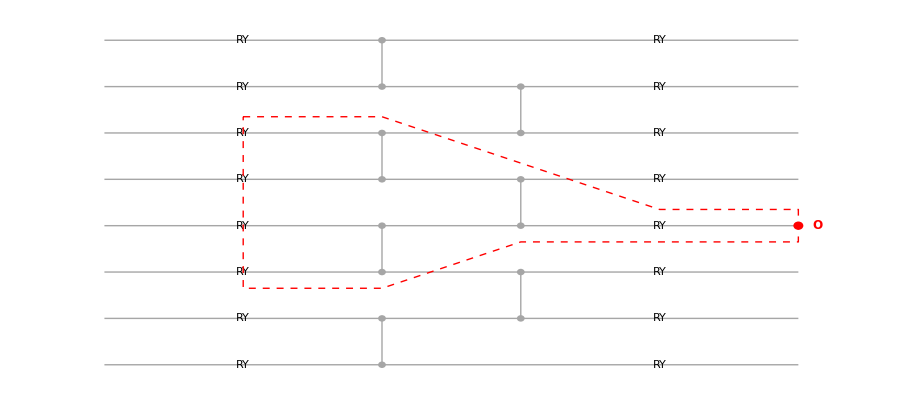

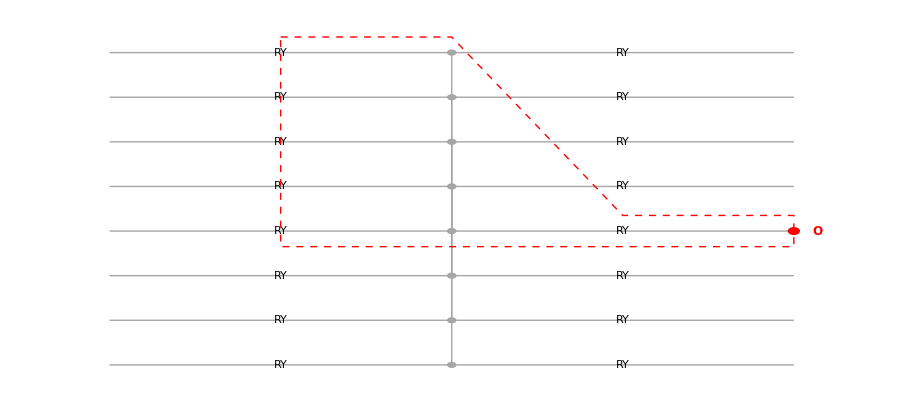

-Graphics- | Métrica | Valor
Observable | q4
Qubits totales | 8
Qubits en el cono | {2,3,4,5}
Tamaño del cono | 4
Fracción del sistema | 0.50
Radio espacial | 2
Profundidad efectiva | 4

-Graphics- | Métrica | Valor
Observable | q4
Qubits totales | 8
Qubits en el cono | {0,4}
Tamaño del cono | 2
Fracción del sistema | 0.25
Radio espacial | 4
Profundidad efectiva | 3

```mathematica
ListaLocal[n_,params_List]:=Module[{θ,ϕ,capa1,capa2,capa3,capa4},θ=Take[params,n];
ϕ=Take[params,{n+1,2 n}];
capa1=Table[<|"Gate"->QuantumOperator["RY"[θ[[j+1]]],{j}],"Qubits"->{j},"Layer"->1,"Label"->"RY"|>,{j,0,n-1}];
(*CZ pares:0-1,2-3,4-5,...*)capa2=Table[<|"Gate"->QuantumOperator["CZ",{j,j+1}],"Qubits"->{j,j+1},"Layer"->2,"Label"->"CZ"|>,{j,0,n-2,2}];
(*CZ impares:1-2,3-4,5-6,...*)capa3=Table[<|"Gate"->QuantumOperator["CZ",{j,j+1}],"Qubits"->{j,j+1},"Layer"->3,"Label"->"CZ"|>,{j,1,n-2,2}];
capa4=Table[<|"Gate"->QuantumOperator["RY"[ϕ[[j+1]]],{j}],"Qubits"->{j},"Layer"->4,"Label"->"RY"|>,{j,0,n-1}];
Join[capa1,capa2,capa3,capa4]]
ListaNoLocal[n_,params_List]:=Module[{θ,ϕ,capa1,capa2,capa3},θ=Take[params,n];
ϕ=Take[params,{n+1,2 n}];
capa1=Table[<|"Gate"->QuantumOperator["RY"[θ[[j+1]]],{j}],"Qubits"->{j},"Layer"->1,"Label"->"RY"|>,{j,0,n-1}];
(*conexiones de largo alcance*)capa2=Table[<|"Gate"->QuantumOperator["CZ",{j,j+Floor[n/2]}],"Qubits"->{j,j+Floor[n/2]},"Layer"->2,"Label"->"CZ"|>,{j,0,Floor[n/2]-1}];
capa3=Table[<|"Gate"->QuantumOperator["RY"[ϕ[[j+1]]],{j}],"Qubits"->{j},"Layer"->3,"Label"->"RY"|>,{j,0,n-1}];
Join[capa1,capa2,capa3]]
params8={θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8};
listaLocal=ListaLocal[8,params8];
listaNoLocal=ListaNoLocal[8,params8];
DibujarConoCausal[listaLocal,{4}]
DibujarConoCausal[listaNoLocal,{4}]
MetricasLocalidad[listaLocal,{4}]
MetricasLocalidad[listaNoLocal,{4}]
MostrarConoCausal[listaLocal,{4}]
MostrarConoCausal[listaNoLocal,{4}]
```

```mathematica
Clear[AnalisisEscalamientoLocalidad]

AnalisisEscalamientoLocalidad[constructorCircuito_,tamanos_List]:=Module[{resultados,n,params,lista,k,datos,qubitsCono,tamano,fraccion,radio,gates,capas,profundidad},resultados=Table[(*Parámetros simbólicos*)params=Join[Array[θ,n],Array[ϕ,n]];
(*Construir circuito*)lista=constructorCircuito[n,params];
(*Observable central*)k=Floor[n/2];
(*Cono causal*)datos=ConoCausal[lista,{k}];
qubitsCono=datos["Qubits"];
gates=datos["GateIndices"];
tamano=Length[qubitsCono];
fraccion=N[tamano/n];
radio=Max[Abs[qubitsCono-k]];
capas=DeleteDuplicates[Lookup[lista[[gates]],"Layer"]];
profundidad=Length[capas];
<|"n"->n,"Observable"->"q"<>ToString[k],"Qubits cono"->qubitsCono,"|LC|"->tamano,"|LC|/n"->fraccion,"Radio"->radio,"Profundidad efectiva"->profundidad|>,{n,tamanos}];
Dataset[resultados]]
AnalisisEscalamientoLocalidad[ListaLocal,{4,6,8,10,12}]
AnalisisEscalamientoLocalidad[ListaNoLocal,{4,6,8,10,12}]
```

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.